```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
<<"MaTeX`"
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

```mathematica
(*Assuming all the legs are made of steel*)
```

```mathematica
(*Similar set of data for 6-RSS has shown that these values are too high*)
```

```mathematica
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.5, la->1.5};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;

(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
(*tpmparam = mtp-> ρ*t*3*√3/2*rt^2/.tplparam/.datap;*)
tpmparam = mtp-> 0.20339;
(*itpz = mtp*rt^2*(1-(2/3)*Sin[π/6]^2);
itpx = itpz/2;
itpy = itpz/2;*)
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;

(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
```

```mathematica
(*Locations of all the known ground joints*)
```

```mathematica
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;
```

```mathematica
tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];
```

```mathematica
b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];
```

```mathematica
al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;
```

```mathematica
tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
```

```mathematica
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
```

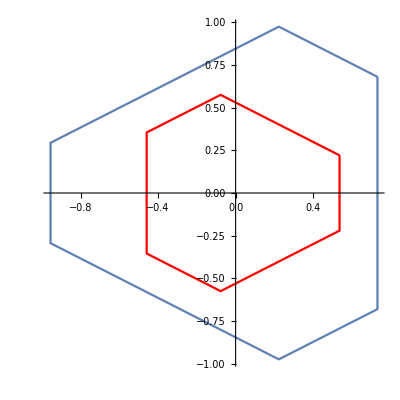

```mathematica
Show[ListLinePlot[Join[(b/.datap), {(b/.datap)[[1]]}][[;;, 1;;2]]],ListLinePlot[Join[(al/.datap), {(al/.datap)[[1]]}][[;;, 1;;2]],PlotStyle->Red], AspectRatio->1]
```

```mathematica
(*Variables*)
```

```mathematica
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
l = Table[Symbol["l"<>ToString[i]],{i,6}];
```

```mathematica
(*Assume the center of the top plate and the orientation as p and R*)
```

```mathematica
pc = {x, y, z};
qq = Join[ϕ, ψ, l];
qx = Join[pc, {c1, c2, c3}];
q = Join[qx, qq];
```

```mathematica
Arp = vec2SkewMat[{c1, c2, c3}];
Rtp = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];
```

```mathematica
(*Checking the orthogonolity of the rotation matrix*)
```

```mathematica
Simplify[Rtp.T[Rtp]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Jvtp = D[pc, {q}];
Jωtp = SkewMat2vec[Simplify[T[Rtp].D[Rtp,{q}]]];
```

```mathematica
(*Formulating the dynamics equations of the manipulator*)
```

```mathematica
(*Finding the Jvp for the ai parts of the links*)
```

```mathematica
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
```

```mathematica
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
```

```mathematica
Jpai = D[pa, {q}];
Jpbi = D[pb, {q}];
```

```mathematica
(*To generate the test data for this system*)
```

```mathematica
qqrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
qxrule = {x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]};
qrule = Join[qxrule,qqrule];
```

```mathematica
(*Angular velocity of any leg li*)
```

```mathematica
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
Jωl = Table[SkewMat2vec[T[Rl[[i]]].D[Rl[[i]],{q}]],{i, 6}];
```

```mathematica
(*Mass Matrix*)
```

```mathematica
tempM = Append[(Table[T[Jpai[[i]]].Jpai[[i]]*ma+T[Jpbi[[i]]].Jpbi[[i]]*mb+T[Jωl[[i]]].Ibi.Jωl[[i]]+T[Jωl[[i]]].Iai.Jωl[[i]],{i, 6}]), T[Jvtp].Jvtp*mtp+T[Jωtp].Itp.Jωtp];
tempM//dim
```

{7,24,24}

```mathematica
tempM2 = Total[tempM, {1}];
tempM2//dim
```

{24,24}

```mathematica
tempM2 - T[tempM2]
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

```mathematica
tempM2//Variables
```

{c1,c2,c3,l1,l2,l3,l4,l5,l6,la,lb,ma,mb,mtp,ri,ro,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
Mmat = Simplify[tempM2/.qrule/.datap/.leglparam/.legmparam/.tpmparam];
```

```mathematica
Mmat//Variables
```

{c1[t],c2[t],c3[t],Cos[2 ψ1[t]],Cos[2 ψ2[t]],Cos[2 ψ3[t]],Cos[2 ψ4[t]],Cos[2 ψ5[t]],Cos[2 ψ6[t]],l1[t],l2[t],l3[t],l4[t],l5[t],l6[t]}

```mathematica
size[Mmat]
```

Size of the expression is:32.2344 KB.

```mathematica
qt = q/.qrule;
```

```mathematica
tic[]
n = Length[qt];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii= 1, ii≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[Mmat[[ii,jj]], qt[[kk]]] + D[Mmat[[ii,kk]], qt[[jj]]] - D[Mmat[[jj, kk]], qt[[ii]]])*D[qt[[kk]],t] ;
kk++];
jj++];
ii++];
toc[]
```

Actual time consumed: 0.216161 seconds.

CPU time consumed: 0.219 seconds.

```mathematica
sampledat = {ϕ1[t]->-0.4120776809584599,ϕ2[t]->-0.5171397464399574,ϕ3[t]->0.17764187369764603,ϕ4[t]->0.28736859806179627,ϕ5[t]->0.19195198975076458,ϕ6[t]->0.3314663928113124,ψ1[t]->-0.010571279864228872,ψ2[t]->0.00656986783518712,ψ3[t]->0.2888385292898862,ψ4[t]->0.45146664507018724,ψ5[t]->-0.32862234369207344,ψ6[t]->-0.5474095601531795,l1[t]->1.0763732914509816,l2[t]->1.3589653226424672,l3[t]->1.3306253991320864,l4[t]->1.3670902994040683,l5[t]->1.1391099344974789,l6[t]->1.163106217592093};
```

```mathematica
initvel = {ϕ1'[t]->0.04819125830959889,ϕ2'[t]->0.03427428403166,ϕ3'[t]->0.022537110420045366,ϕ4'[t]->-0.02504333390626954,ϕ5'[t]->-0.06015570745871055,ϕ6'[t]->-0.06962346394226754,ψ1'[t]->0.17522543152669445,ψ2'[t]->0.09442759444255354,ψ3'[t]->0.05971195202706652,ψ4'[t]->0.04189876317323693,ψ5'[t]->0.08197436457283205,ψ6'[t]->0.1734108446847269,l1'[t]->0.1,l2'[t]->0,l3'[t]->0,l4'[t]->0,l5'[t]->0,l6'[t]->0};
```

```mathematica
Mmatdat = D[Mmat, t];
tempA = Mmatdat-2*tempC;
temppA = tempA+T[tempA];
temppA//dim
Chop[Simplify[temppA]]
```

{24,24}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(*Formulating the potential term*)
```

```mathematica
tempV = Table[{ma*g*pa[[i]][[3]], mb*g*pb[[i]][[3]]},{i, 6}];
```

```mathematica
V = Total[Append[Flatten[tempV], mtp*g*pc[[3]]]]/.datap/.leglparam/.legmparam/.tpmparam;
G = D[V, {q}];
```

```mathematica
Variables[G]
```

{l1,l2,l3,l4,l5,l6,Cos[ϕ1],Cos[ϕ2],Cos[ϕ3],Cos[ϕ4],Cos[ϕ5],Cos[ϕ6],Cos[ψ1],Cos[ψ2],Cos[ψ3],Cos[ψ4],Cos[ψ5],Cos[ψ6],Sin[ϕ1],Sin[ϕ2],Sin[ϕ3],Sin[ϕ4],Sin[ϕ5],Sin[ϕ6],Sin[ψ1],Sin[ψ2],Sin[ψ3],Sin[ψ4],Sin[ψ5],Sin[ψ6]}

```mathematica
(*Now we have dynamics in the extended configuration space. We need to map it back to the task space of the manipulator*)
```

```mathematica
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating the simple constraint equations (not the rigidity of the top platform constraint)*)
```

```mathematica
η = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};
```

```mathematica
alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];
```

```mathematica
atps = Table[pc+Rtp.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
(*ηleg = Table[Together[((atps-b)[[i]]).((atp-b)[[i]])-l[[i]]^2],{i, 6}];*)
```

```mathematica
(*ηtask = Join[η, ηleg]/.alsrules/.bsrules/.datap;*)
```

```mathematica
(*ηtask//Dimensions
ηtask//Variables*)
```

```mathematica
θ = q[[-6;;]]
```

{l1,l2,l3,l4,l5,l6}

```mathematica
qex = q[[;;-7]]
```

{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6}

```mathematica
Jηqx = D[η, {qex}];
Jηθ =D[η, {θ}];
```

```mathematica
(*Assuming the working of the manipulator in SWZ and also not having Jηq singularity anywhere. Interesting that this map demands Jηq Jacobians existence and not Jηϕ*)
```

```mathematica
(*Since the matrix is sparse, try symbolic inverse some other time*)
```

```mathematica
dϕ = Table[Symbol["dϕ"<>ToString[i]],{i, 6}];
dψ = Table[Symbol["dψ"<>ToString[i]],{i, 6}];
dl = Table[Symbol["dl"<>ToString[i]],{i, 6}];
dq = Join[dϕ, dψ,dl];
dqrule = Inner[Rule, D[qq/.qrule, t], dq, List];
rqϕrule= Join[Inner[Rule,qq/.qrule, qq, List], dqrule];
rxrule = Inner[Rule, qx/.qrule, qx, List];
drxrule = Inner[Rule, D[qx/.qrule, t], {dx, dy, dz, dc1, dc2, dc3}, List];
rqrule = Join[rxrule, drxrule, rqϕrule];
```

```mathematica
cJηqx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[Jηqx]];
```

```mathematica
dJηqx = D[Jηqx/.qrule, t]/.rqrule;
cdJηqx= Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηqx]];
```

```mathematica
cJηθ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[Jηθ]];
```

```mathematica
dJηθ = D[Jηθ/.qrule, t]/.rqrule;
cdJηθ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηθ]];
```

```mathematica
tMmat = TrigExpand[Mmat/.rqrule];
cMmat = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tMmat]];
```

```mathematica
tCmat = TrigExpand[Simplify[tempC/.rqrule]];
cCmat = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[tCmat]];
```

```mathematica
cGvec = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[G]];
```

```mathematica
(*IK module for the manipulator*)
```

```mathematica
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cψval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
```

```mathematica
cϕval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksol[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]
```

```mathematica
trigrules = (Join[sinϕrule/.Inner[Rule, Cos[ψ], cosψ, List]/.lirule/.bsrules/.alsrules/.datap, cosϕrule/.Inner[Rule, Cos[ψ], cosψ, List]/.lirule/.bsrules/.alsrules/.datap, sinψrule/.lirule/.bsrules/.alsrules/.datap, cosψrule/.lirule/.bsrules/.alsrules/.datap, lirule/.bsrules/.datap]);
```

```mathematica
cη = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[Simplify[η]]];
```

```mathematica
qval = {0,0,1.1,0,0,0};
```

```mathematica
qesample = Join[qval, iksol[qval]];
```

```mathematica
(*Root-tracking*)
```

```mathematica
TrackRoot[thetai_, phii_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
nvec = cη@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Max[Abs[nvec]]≥ 10^-15,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  cJηqx@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = cη@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
tempϕ = qesample[[;;-7]];
doubledots[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{Mval, Cval, Gval, LHS,Jηθval, Jηqxval, Jqxθval,Jqeθval, Mθval, dMmatval, Cθval, Gθval, dJηθval, dJηqxval, dJqeθval, dqe, qe},
(*Perform root-tracking to get the passive variable data*)
tempϕ = TrackRoot[q, tempϕ];
qe = Join[tempϕ, q];
(*Getting the velocities of the configuration space variables*)
Jηθval = cJηθ@@qe;
Jηqxval = cJηqx@@qe;
Jqxθval = -Inverse[Jηqxval].Jηθval;
dqe = Join[Jqxθval.dq, dq];
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηqxval = cdJηqx@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jqxθval}, {IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηqxval].(-dJηqxval.Inverse[Jηqxval].Jηθval+dJηθval)}, {ConstantArray[0,{6,6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*LHS of the dynamics equations*)
LHS = -(Inverse[Mθval]).(Cθval.dq+Gθval);
Return[LHS];
];
```

```mathematica
qval = {0,0,1.1,0,0,0};
dqval = {0,0,0,0,0,0};
```

```mathematica
qθval = qesample[[-6;;]];
dqθval = {0,0,0,0,0,0};
```

```mathematica
doubledots[qθval, dqθval]
```

{-9.1338,-9.13383,-9.13378,-9.13378,-9.13383,-9.1338}

```mathematica
(*There is some problem with finding the velocity of the configuration space variables from the task space velocities*)
```

```mathematica
PortMattoC[tempϕ]
```

PortMattoC[{0,0,1.1,0,0,0,-0.17618,-0.266725,0.423902,0.423902,-0.266725,-0.17618,0.390648,0.337095,-0.0500618,0.0500618,-0.337095,-0.390648}]

```mathematica
tempϕ = qesample[[;;-7]];
tic[]
dynsim = NDSolve[{doubledots[q1[t],q1'[t]]==q1''[t],q1[0]==qθval,q1'[0]==dqθval},q1,{t,0,0.48},Method->"Adams"(*, AccuracyGoal->15*)]
toc[]
```

{{q1→InterpolatingFunction[…]}}

Actual time consumed: 1.040837 seconds.

CPU time consumed: 0.313 seconds.

```mathematica
(*loop closure in completely task space variables*)
ηeqn = η/.trigrules/.datap/.leglparam/.legmparam/.tpmparam;
```

```mathematica
(*Now performing the energy checks needed*)
```

```mathematica
qsol = (q1/.dynsim)[[1]];
```

```mathematica
(*Since all the checks are already present in task space, track the task space variables*)
```

```mathematica
Clear[qinit, qlist, qinitnew]
qinit = qesample[[;;-7]];
qlist = {Join[qinit, qsol[0]]};
For[i=0.01, i≤0.45, i=i+0.01, 
qinit = TrackRoot[qsol[i], qinit];
AppendTo[qlist, Join[qinit, qsol[i]]];
]
```

```mathematica
dqac = Table[qsol'[i],{i, 0, 0.45, 0.01}];
```

```mathematica
dqmod[qf_?(VectorQ[#,NumericQ]&), dqf_?(VectorQ[#,NumericQ]&)]:=Module[{Jηθval, Jηqxval, Jqxθval},
Jηθval = cJηθ@@qf;
Jηqxval = cJηqx@@qf;
Jqxθval = -Inverse[Jηqxval].Jηθval;
Return[Join[Jqxθval.dqf, dqf]];
]
```

```mathematica
dqlist = Table[dqmod[qlist[[ii]], dqac[[ii]]], {ii, Length[qlist]}];
```

```mathematica
qxlist = qlist[[;;,;;6]];
dqxlist = dqlist[[;;,;;6]];
```

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->All,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize, PlotRange->All];

Return[f1nonsing];
]
```

```mathematica
(*1. Zeroth order check: Checking the norm of the loop closure througout the motion*)
```

```mathematica
time = Table[t, {t, 0, 0.45, 0.01}];
```

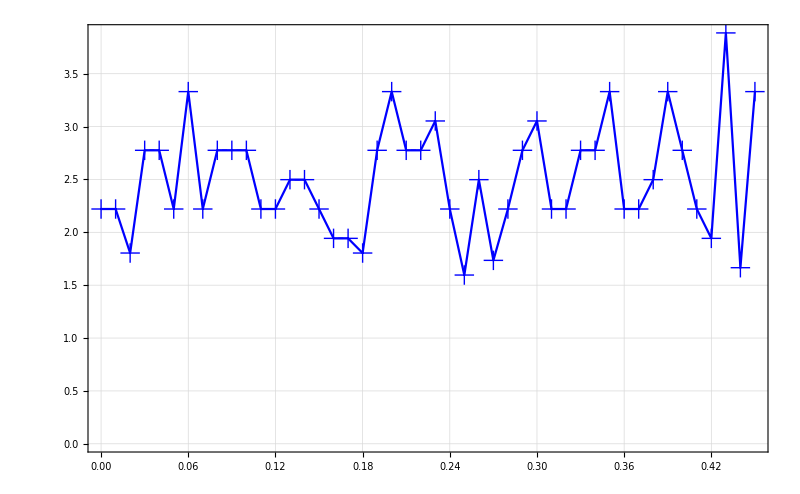

```mathematica
ηtest = Table[Max[Abs[ηeqn/.Inner[Rule,qx,qxlist[[i]], List]]],{i, 1, Length[qxlist]}];
Texplot[time, ηtest*10^16, 800, "Time~(s)", "e_1 (\\times 10^{-16})"]
```

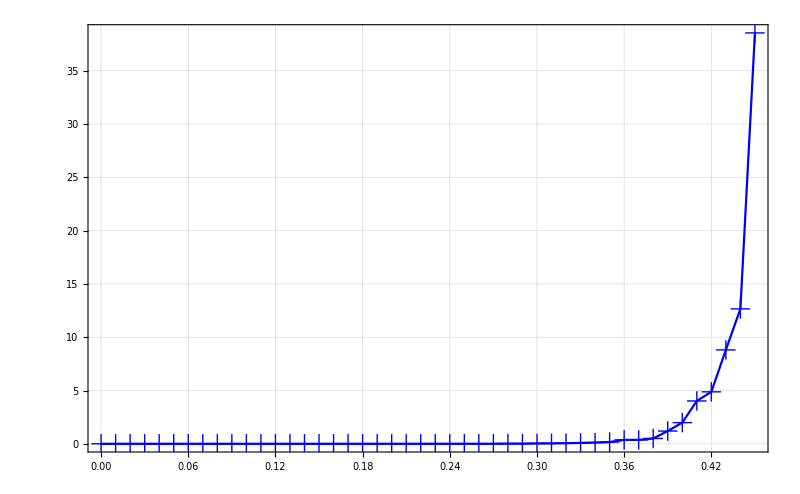

```mathematica
(*2. First order check: Checking the norm of Jηq.q' check*)
Jηeqnx = D[ηeqn, {qx}];
cJηeqnx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[Jηeqnx]];
Jηeqnxtest = Table[Max[Abs[cJηeqnx@@qxlist[[i]].dqxlist[[i]]]],{i,1, Length[qxlist]}];
Texplot[time, Jηeqnxtest*10^23, 800, "Time~(s)", "e_2 (\\times 10^{-23})"]
```

```mathematica
(*3. Second order check: Cheking norm of Jηq.d2q+dJηq.dq*)
dJηeqnx = D[Jηeqnx/.qrule, t];
dJηeqnx2 = dJηeqnx/.rqrule;
```

```mathematica
cdJηeqnx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}}, Evaluate[dJηeqnx2]];
```

```mathematica
(*dJηeqnxtest = Table[Norm[cJηeqnx@@qsol[i].qsol''[i]+cdJηeqnx@@Join[qsol[i], qsol'[i]].qsol'[i]],{i, 0, 1, 0.01}];
Texplot[time, dJηeqnxtest*10^20, 800, "Time~(s)", "e_3 (\\times 10^{-20})"]*)
```

```mathematica
(*To check Energy remove the applied external torque*)
(*4. Energy: Checking Energy constant criteria*)
Vsubs = V/.trigrules/.bsrules/.alsrules/.datap/.leglparam/.legmparam/.tpmparam;
Msubs = TrigExpand[Mmat]/.rqrule/.trigrules/.bsrules/.alsrules/.datap/.leglparam/.legmparam/.tpmparam;
Vlist = Table[Vsubs/.Inner[Rule,qx, qxlist[[i]], List], {i, 1, Length[qxlist]}];
Mlist = Table[Msubs/.Inner[Rule,qx, qxlist[[i]], List], {i, 1,Length[qxlist]}];
qfull = qlist;
```

```mathematica
Jηq = D[η, {qq}];
Jηx = D[η, {qx}];
```

```mathematica
Jηqtab = Table[Jηq/.Inner[Rule, q, qfull[[i]], List],{i, Length[qfull]}];
Jηxtab = Table[Jηx/.Inner[Rule, q, qfull[[i]], List],{i, Length[qfull]}];
```

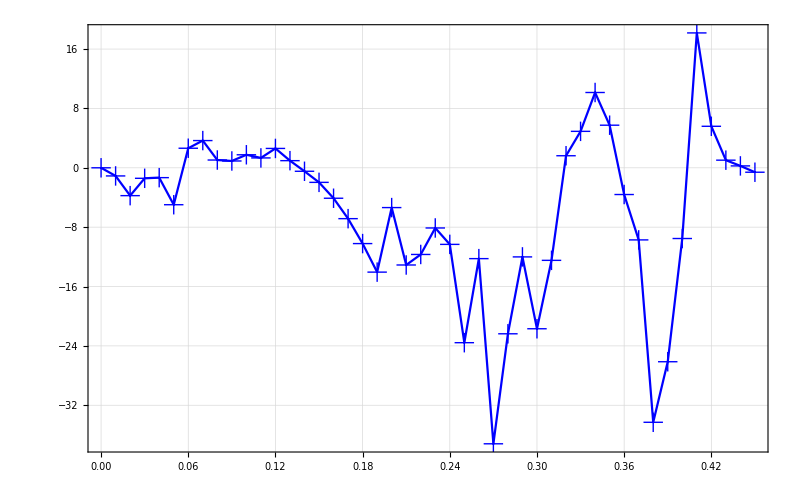

```mathematica
Jqxtab = Table[-Inverse[Jηqtab[[i]]].Jηxtab[[i]], {i, Length[qfull]}];
dq2 = dqxlist;
dqtab = Table[Join[dq2[[i]], Jqxtab[[i]].dq2[[i]]],{i, Length[dq2]}];
Hlist = Table[1/2*(dqtab[[i]].Mlist[[i]].dqtab[[i]])+Vlist[[i]],{i, Length[dq2]}];
H1 = ConstantArray[Hlist[[1]], Dimensions[Hlist]];
Texplot[time,(Hlist-H1)/H1*10^8, 800, "Time~(s)", "e_3 (\\times 10^{-8})"]
```

```mathematica
qfullrules = Table[Inner[Rule, q, qfull[[ii]], List], {ii, 1, Length[qfull]}];
```

```mathematica
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.3, 1.3}, {-1.3, 1.3}, {-1.3, 1.3}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
(*llinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],aval[[i]]/.qvals}, 0.04]}],{i, Length[bval]}];*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
lainks = Table[Graphics3D[{LightOrange,Opacity[0.5],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
(*Plotting the configuration*)
Show[base, top, jointstop, jointsbase, lainks, lbinks]]
```

```mathematica
(*plotsrspm[testpose]*)
```

```mathematica
(*Export["image.pdf",image,ImageResolution->600]*)
```

```mathematica
mansrspm = Manipulate[
plotsrspm[qfullrules[[j]]],
{j, 1, Length[qfullrules], 1}, ContentSize->{400,400}]
```

```mathematica
(*Extended mapped to actuator-space is working. So mapping it to Cpp*)
```

```mathematica
trigrep[i_]:={Cos[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[lambda]<>ToString[i]]],Sin[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ToExpression[Symbol[ToString[mu]<>ToString[i]]],Sec[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]]),Csc[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> 1/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]),Tan[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[mu]<>ToString[i]]])/(ToExpression[Symbol[ToString[lambda]<>ToString[i]]])),Cot[ToExpression[Symbol[ToString[α]<>ToString[i]]]]-> ((ToExpression[Symbol[ToString[lambda]<>ToString[i]]])/(ToExpression[Symbol[ToString[mu]<>ToString[i]]]))};
alpharep[i_]:={ToExpression[Symbol[ToString[α]<>ToString[i]]]-> ToExpression[Symbol[ToString[alpha]<>ToString[i]]]};
alpharepall=Union[alpharep[1],alpharep[2],alpharep[3],alpharep[4],alpharep[5],alpharep[6]];
revtrigrep[i_]:=Reverse[trigrep[i],2];
trigrepall=Union[trigrep[1],trigrep[2],trigrep[3],trigrep[4],trigrep[5],trigrep[6]];
revtrigrepall=Union[revtrigrep[1],revtrigrep[2],revtrigrep[3],revtrigrep[4],revtrigrep[5],revtrigrep[6]];
revreplist=Reverse[replist,2];
revalpharepall=Reverse[alpharepall,2];
inversetrig =  Union[{ArcTan[x_, y_]->atan2[y,x]} , {ArcCos[x_]->acos[x]}];
replist=Union[{Power-> pow},trigrepall,{Sin[x_]-> sin[x]},{Cos[x_]-> cos[x]},{Tan[x_]-> tan[x]},{Csc[x_]-> 1/sin[x]},{Sec[x_]-> 1/cos[x]},{Cot[x_]->sin[x]/cos[x]}];
Print["Change the angles from Greek symbols"]
```

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[replist,2].

Change the angles from Greek symbols

```mathematica
phi = Table[Symbol["p"<>ToString[i]],{i, 6}];
psi = Table[Symbol["s"<>ToString[i]],{i, 6}];
dphi = Table[Symbol["dp"<>ToString[i]],{i, 6}];
dpsi = Table[Symbol["ds"<>ToString[i]],{i, 6}];
nogreek = Join[Inner[Rule, ϕ, phi, List], Inner[Rule, ψ, psi, List], Inner[Rule, dϕ, dphi, List], Inner[Rule, dψ, dpsi, List]];
```

```mathematica
cospsi = Table[Symbol["cs"<>ToString[i]],{i, 6}];
sinpsi = Table[Symbol["ss"<>ToString[i]],{i, 6}];
cosphi = Table[Symbol["cp"<>ToString[i]],{i, 6}];
sinphi = Table[Symbol["sp"<>ToString[i]],{i, 6}];
```

```mathematica
trigtoalg = Join[Inner[Rule, Cos[ψ], cospsi, List], Inner[Rule, Sin[ψ], sinpsi, List], Inner[Rule, Cos[ϕ], cosphi, List], Inner[Rule, Sin[ϕ], sinphi, List]];
```

```mathematica
(*Exporting the matrices to C++*)
```

```mathematica
(*PortMattoC[mat_]:=Module[{tempMattoC, mattoC},
(*Substitute all Greek letters and flatten matrices into vectors*)
tempMattoC = Flatten[mat]/.trigtoalg/.replist/.inversetrig/.nogreek;
mattoC  = StringTake[ToString[Table[CForm[tempMattoC[[i]]],{i, Length[tempMattoC]}]],{2,-2}];
Return [mattoC];
]*)
```

```mathematica
(*redrule = Inner[Rule, {cos[2 s1], cos[2 s2],cos[2 s3],cos[2 s4], cos[2 s5],cos[2 s6]}, {cs21, cs22, cs23, cs24, cs25, cs26}, List];
tMmat2 = Simplify[tMmat]/.trigtoalg/.replist/.nogreek/.redrule/.inversetrig;*)
```

```mathematica
(*MmattoC = PortMattoC[tMmat2];
CmattoC = PortMattoC[tCmat];
GmattoC = PortMattoC[G];*)
```

```mathematica
(*JηqxtoC = PortMattoC[Jηqx];
JηθtoC = PortMattoC[Jηθ];*)
```

```mathematica
(*dJηqxtoC = PortMattoC[dJηqx];
dJηθtoC = PortMattoC[dJηθ];*)
```

```mathematica
(*ηtoc = PortMattoC[η];*)
```

```mathematica
(*file = Import["dyn_funcs.h", "Text"];*)
```

```mathematica
(*FileTemplateApply[file,<|"Mexpressions1"->MmattoC, "Cexpressions1"->CmattoC, "Gexpressions1"->GmattoC,"Jetaqphiexpressions1"->JηqxtoC, "Jetaqthexpressions1"->JηθtoC, "dJetaqphiexpressions1"->dJηqxtoC, "dJetaqthexpressions1"->dJηθtoC,"etaexpressions1"->ηtoc|>, "CPP/dyn_funcs_test.h"];*)
```

```mathematica
(*Jηl = D[η, {q[[-6;;]]}];*)
```

```mathematica
(*Jηϕe = D[η, {q[[;;-7]]}];*)
```

```mathematica
(*vels = Inverse[Jηϕe/.testpose].(Jηl/.testpose).{0.1,0,0,0,0,0}*)
```

```mathematica
(*fullvel = Join[vels, {0.1,0,0,0,0,0}];*)
```

```mathematica
(*dfullq = Join[{dx, dy, dz, dc1, dc2, dc3},dq]*)
```

```mathematica
(*fullvel  = Inner[Rule, dfullq, fullvel, List]*)
```

```mathematica
(*testpose*)
```

```mathematica
(*PortMattoC[dJηx/.testpose/.fullvel]*)
```

```mathematica
TrackRoot[thetai_, phii_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
nvec = cη@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Max[Abs[nvec]]≥ 10^-15,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  cJηqx@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = cη@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
(*Verifying the data generated by the cpp codes*)
(*Verifying the C++ data*)

qxdat = Import["qxdata.dat"];
dqxdat = Import["dqxdata.dat"];
dddat = Import["dddata.dat"];
```

```mathematica
qllist = qxdat[[;;, 2;;]];
dqllist = dqxdat[[;;, 2;;]];
ddqllist = dddat[[;;, 2;;]];
```

```mathematica
Clear[qinit, qlist, qinitnew, i]
qinit = qesample[[;;-7]];
qlist = {Join[qinit, qllist[[1]]]};
For[i=2, i≤Length[qllist], i++, 
qinit = TrackRoot[qllist[[i]], qinit];
AppendTo[qlist, Join[qinit, qllist[[i]]]];
]
```

```mathematica
dqmod[qf_?(VectorQ[#,NumericQ]&), dqf_?(VectorQ[#,NumericQ]&)]:=Module[{Jηθval, Jηqxval, Jqxθval},
Jηθval = cJηθ@@qf;
Jηqxval = cJηqx@@qf;
Jqxθval = -Inverse[Jηqxval].Jηθval;
Return[Join[Jqxθval.dqf, dqf]];
]
```

```mathematica
dqlist = Table[dqmod[qlist[[ii]], dqllist[[ii]]], {ii, Length[qlist]}];
```

```mathematica
qxlist = qlist[[;;,;;6]];
dqxlist = dqlist[[;;,;;6]];
```

```mathematica
(*1. Zeroth order check: Checking the norm of the loop closure througout the motion*)
```

```mathematica
time = Table[t, {t, 0, 0.45, 0.01}];
```

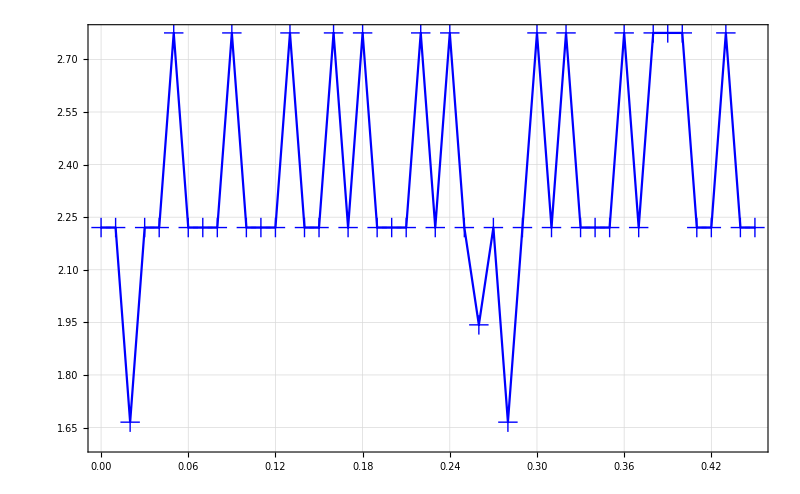

```mathematica
ηtest = Table[Max[Abs[ηeqn/.Inner[Rule,qx,qxlist[[i]], List]]],{i, 1, Length[qxlist]}];
Texplot[time, ηtest*10^16, 800, "Time~(s)", "e_1 (\\times 10^{-16})"]
```

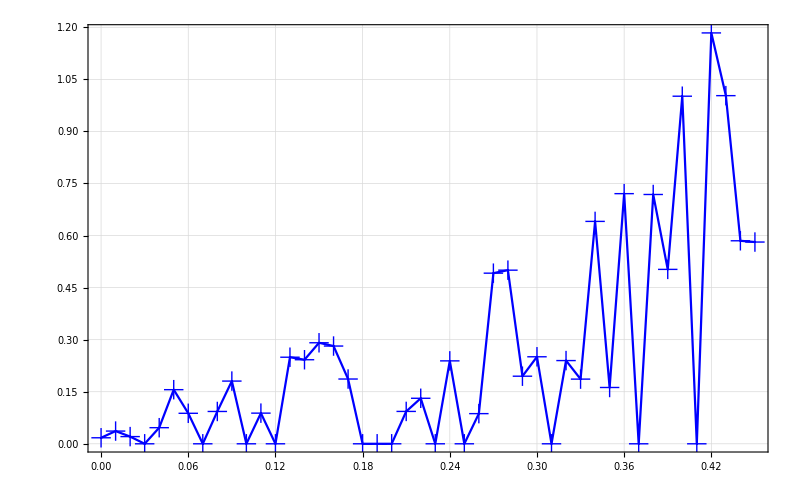

```mathematica
(*2. First order check: Checking the norm of Jηq.q' check*)
Jηeqnx = D[ηeqn, {qx}];
cJηeqnx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[Jηeqnx]];
Jηeqnxtest = Table[Max[Abs[cJηeqnx@@qxlist[[i]].dqxlist[[i]]]],{i,1, Length[qxlist]}];
Texplot[time, Jηeqnxtest*10^31, 800, "Time~(s)", "e_2 (\\times 10^{-31})"]
```

```mathematica
(*3. Second order check: Cheking norm of Jηq.d2q+dJηq.dq*)
dJηeqnx = D[Jηeqnx/.qrule, t];
dJηeqnx2 = dJηeqnx/.rqrule;
```

```mathematica
cdJηeqnx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}}, Evaluate[dJηeqnx2]];
```

```mathematica
(*dJηeqnxtest = Table[Norm[cJηeqnx@@qsol[i].qsol''[i]+cdJηeqnx@@Join[qsol[i], qsol'[i]].qsol'[i]],{i, 0, 1, 0.01}];
Texplot[time, dJηeqnxtest*10^20, 800, "Time~(s)", "e_3 (\\times 10^{-20})"]*)
```

```mathematica
(*To check Energy remove the applied external torque*)
(*4. Energy: Checking Energy constant criteria*)
Vsubs = V/.trigrules/.bsrules/.alsrules/.datap/.leglparam/.legmparam/.tpmparam;
Msubs = TrigExpand[Mmat]/.rqrule/.trigrules/.bsrules/.alsrules/.datap/.leglparam/.legmparam/.tpmparam;
Vlist = Table[Vsubs/.Inner[Rule,qx, qxlist[[i]], List], {i, 1, Length[qxlist]}];
Mlist = Table[Msubs/.Inner[Rule,qx, qxlist[[i]], List], {i, 1,Length[qxlist]}];
qfull = qlist;
```

```mathematica
Jηq = D[η, {qq}];
Jηx = D[η, {qx}];
```

```mathematica
Jηqtab = Table[Jηq/.Inner[Rule, q, qfull[[i]], List],{i, Length[qfull]}];
Jηxtab = Table[Jηx/.Inner[Rule, q, qfull[[i]], List],{i, Length[qfull]}];
```

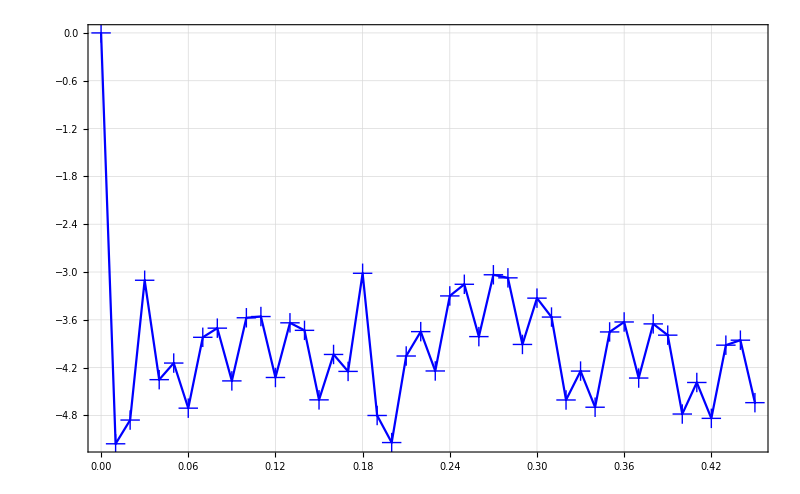

```mathematica
Jqxtab = Table[-Inverse[Jηqtab[[i]]].Jηxtab[[i]], {i, Length[qfull]}];
dq2 = dqxlist;
dqtab = Table[Join[dq2[[i]], Jqxtab[[i]].dq2[[i]]],{i, Length[dq2]}];
Hlist = Table[1/2*(dqtab[[i]].Mlist[[i]].dqtab[[i]])+Vlist[[i]],{i, Length[dq2]}];
H1 = ConstantArray[Hlist[[1]], Dimensions[Hlist]];
Texplot[time,(Hlist-H1)/H1*10^5, 800, "Time~(s)", "e_3 (\\times 10^{-5})"]
```